```mathematica
(* Generation of weight functions for Becke integration scheme *)
BeckeP[x_]:=3/2*x - 1/2*x^3
BeckeF3[x_]:=BeckeP[BeckeP[BeckeP[x]]]
BeckeWeighti[x_]:=1/2*(1-BeckeF3[x])
```

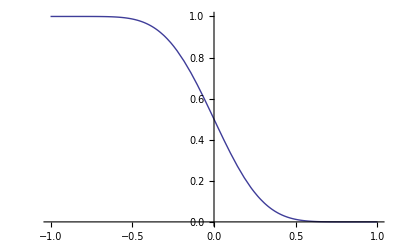

```mathematica
Plot[BeckeWeighti[x],{x,-1,1}]
```

```mathematica
(* Becke single center atomic integrals *)
```